Estimação: estimar um parâmetro a partir de uma estatística.

Para uma estatística medida de uma amostra, há uma chance de esta estatística corresponder ao parâmetro.

Primeiro, o valor provável do parâmetro é centrado no valor da estatística.
O valor real do parâmetro é um intervalo em torno deste centro.

A largura do intervalo é maior quanto menor a precisão sobre o valor do parâmetro, pois, quanto menor a certeza sobre o valor real de uma incógnica, mais larga a faixa de valores que esta incógnita pode admitir.

A precisão do valor do parâmetro varia com a variância colhida na amostra. Quanto maior a variância, menor a precisão, pois uma amostra mais variável indica uma aproximação menos certa sobre o valor lido.

A probabilidade de a estatística corresponder ao parâmetro acompanha uma distribuição normal, pois no centro há o valor colhido da estatística; e, para ambos os lados, a probabilidade crescentemente menor de que o valor real esteja mais distante deste centro.

Ao calcular um intervalo, centramos o valor provável do parâmetro na estatística e escolhemos a probabilidade ou margem de acerto ou erro sobre o valor do parâmetro. Quanto menor a margem de erro desejada, maior será o intervalo aferido, pois temos mais certeza quanto mais abrangente nossa estimativa. Quanto maior a margem de erro admitida, menor será o intervalo aferido, pois podemos obter um valor mais preciso ao admitir mais chance que ele esteja incorreto.
A variância altera a curva de probabilidade a partir da qual tiraremos os pontos; quanto menor a variância, mais área, ou seja, maior probabilidade, de o valor estar mais próximo ao centro, ou ao valor da estatística; portanto a curva é mais acentuada, com mais área em torno do centro. Quanto maior a variância, mais probabilidade de o valor estar mais distante do centro, portanto a curva é menos acentuada no centro (o que confere mais probabilidade aos pontos mais distantes do centro).

```mathematica
Manipulate[Plot[PDF[NormalDistribution[0,σ],x],{x,-3,3},ImageSize->250,PlotTheme->"Minimal"],{{σ,1},0.35,1.5,0.1}]
```

Ao calcular um intervalo, lemos a amostra, escolhemos uma precisão, e obtemos o intervalo de valor do parâmetro.

Ao testar uma hipótese, escolhemos um valor, lemos a amostra e obtemos a precisão. Se a precisão corresponde (ou não) a um intervalo de precisão estipulado para afirmar que o valor está previsto ou não nesta precisão para esta amostra, o teste é dito aceito ou recusado.

#### The curve

Think about expressing a function of decreasing probability around a number.
This is what you possibly get:

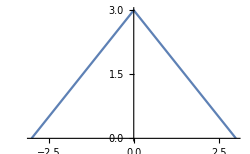

```mathematica
Plot[-Abs[x]+3,{x,-3,3},ImageSize->250,PlotTheme->"Minimal"]
```

Now, smooth it:

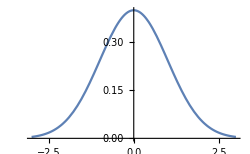

```mathematica
Plot[PDF[NormalDistribution[],x],{x,-3,3},ImageSize->250,PlotTheme->"Minimal"]
```

The probability is the ‘piece’ of the object formed in the intersection of the curve with the horizontal axis:
(piece of normal curve)

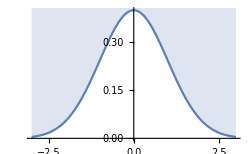

```mathematica
Plot[PDF[NormalDistribution[],x],{x,-3,3},ImageSize->250,PlotTheme->"Minimal",Filling->.5]
```

The piece is bigger the higher its upper limit is for the same piece width; in this curve shape, it is simmetrically around the point in the center. This is so because we don’t estimate any reason why the number in the population (the parameter) is with higher probability any particular number other than: probably the statistic number, and with smooth decreasing probability to both sides, a number farther away.
The bigger the pieces in a certain area of the object, the higher the probability any arbitrary piece in the object is in that area.

This measurement is the area under the curve of the probability function f and is pre-computed in inferential statistics, to have us not need compute the integral, since the curves are common. These values are provided in z-tables for common curves such as the normal curve and other distribution curves.

Curvas diferentes são usadas em situações diferentes para estimar parâmetros. (...)